```mathematica
planFloor[{gh_, gv_}, area_, α_, s_] := 
 Block[{n, rids = Union[VertexList[gh], VertexList[gv]], 
   areas = area, elh = EdgeList[gh], elv = EdgeList[gv], x, w, W, y, 
   h, H, xall, wall, yall, hall},
  n = Length[rids];
  If[NumberQ[area], areas = ConstantArray[area, n]];
  horizontalConstraints = positionConstraints[gh, x, w, W, s, rids];
  verticalConstraints = positionConstraints[gv, y, h, H, s, rids];
  xall = Map[x, rids];
  wall = Map[w, rids];
  yall = Map[y, rids];
  hall = Map[h, rids];
  aspectConstraints = {VectorLessEqual[{hall, α wall}], 
    VectorLessEqual[{wall, α hall}]};
  positivityConstraints = {VectorGreaterEqual[{xall, 0}], 
    VectorGreaterEqual[{hall, 0}], VectorGreaterEqual[{yall, 0}], 
    VectorGreaterEqual[{wall, 0}]};
  (* Use Schur complements to express h*w≥a convexely *)
    areaConstraints = MapThread[Function[{{#1, #3}, {#3, #2}} 
(\[VectorGreaterEqual])_ 0], {wall, hall, Sqrt[areas]}];
  rules = 
   SemidefiniteOptimization[
    H + W, {horizontalConstraints, verticalConstraints, 
     aspectConstraints, positivityConstraints, areaConstraints}, 
    Flatten[{H, W, xall, wall, yall, hall}]];
  {Rectangle[{0, 0}, {W, H}] /. rules, 
   AssociationMap[
    Function[
     Rectangle[{x[#], y[#]}, {x[#] + w[#], y[#] + h[#]}] /. rules], 
    rids]}]
```

```mathematica
positionConstraints[g_,x_,w_,W_,s_,rids_]:=Module[{u,l,cp,cl,cu,edgeConstraint},u[_]=True;
l[_]=True;
edgeConstraint[DirectedEdge[i_,j_]]:=(u[i]=False;l[j]=False;x[i]+w[i]+s<=x[j]);
cp=Map[edgeConstraint,EdgeList[g]];
cl=Table[If[l[r],x[r]>=0,Nothing],{r,rids}];
cu=Table[If[u[r],x[r]+w[r]<=W,Nothing],{r,rids}];
Join[cp,cl,cu]];
```

```mathematica
hg=Graph[Range[10],{1->2,1->3,1->4,1->5,1->6,1->7,2->3,4->5,2->3,2->5,2->7,4->3,4->5,4->7,6->5,8->4,9->4,10->4,10->6,6->7,8->9,8->10}];
vg=Graph[Range[10],{1->6,1->7,1->8,1->9,1->10,2->4,2->9,4->6,3->5,5->7,9->10}];
```

```mathematica
areas=ConstantArray[100.,10];
areas[[1]]=400.;
```

```mathematica
{big,little}=planFloor[{hg,vg},areas,2,1]
```

{Rectangle[{0,0},{40.7334,36.1625}],<|1→Rectangle[{1.37447×10^-9,5.24901×10^-10},{21.1703,18.8944}],2→Rectangle[{22.1703,6.8036×10^-9},{30.9519,11.3875}],3→Rectangle[{31.9519,6.80303×10^-9},{40.7334,11.3875}],4→Rectangle[{22.1703,12.3875},{30.9519,23.775}],5→Rectangle[{31.9519,12.3875},{40.7334,23.775}],6→Rectangle[{22.1703,24.775},{30.9519,36.1625}],7→Rectangle[{31.9519,24.775},{40.7334,36.1625}],8→Rectangle[{-4.76329×10^-10,21.0063},{7.07107,35.1484}],9→Rectangle[{8.07107,19.8944},{21.1703,27.5284}],10→Rectangle[{8.07107,28.5284},{21.1703,36.1625}]|>}

```mathematica
rkey[key_,r:Rectangle[ll_,ur_]]:={LightBlue,r,Black,Text[ToString[key],(ll+ur)/2]};
```

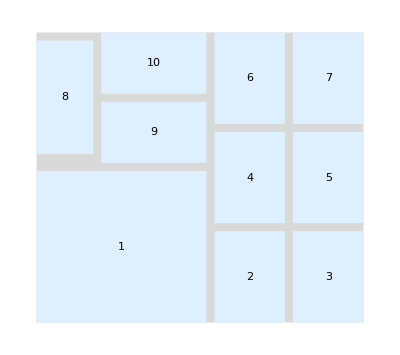

```mathematica
Graphics[{{LightGray,big},MapThread[rkey,{Keys[little],Values[little]}]}]
```

```mathematica
Map[RegionMeasure,Values[little]]
```

{400.,100.,100.,100.,100.,100.,100.,100.,100.,100.}

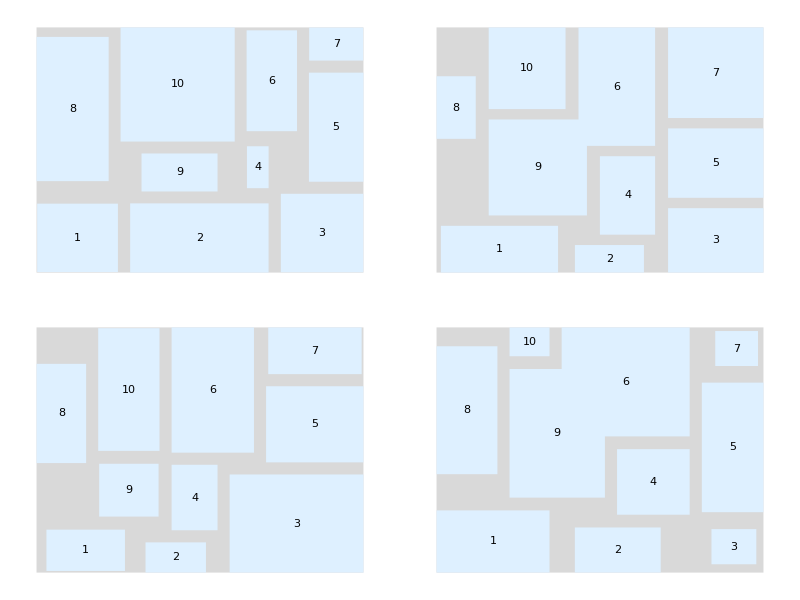

```mathematica
Grid[Table[{big,little}=planFloor[{hg,vg},RandomReal[1,10],2,.1];
Graphics[{{LightGray,big},MapThread[rkey,{Keys[little],Values[little]}]}],{2},{2}]]
```